```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
aUpper=3;
```

## Michaelis-Menten

```mathematica
fSolveSystem[aSeries_Integer,system__,lVars__,lParams__,aTMax_]:=Block[{lSols},lSols=Flatten@NDSolve[system,lVars,{t,0,aTMax}];lSols[[aSeries,2]]]
fSolveSystemAll[aSeries_Integer,system__,lVars__,lParams__,aTMax_]:=Block[{lSols},lSols=Flatten@NDSolve[system,lVars,{t,0,aTMax}];lSols[[All,2]]]
fCalculateF[system__,lParams__,aNumVars_Integer]:=D[system[[1;;aNumVars,2]],#]&/@lParams
fSensitivity[aSeries_Integer,aParam_Integer,system__,mF__,lVars__,lParams__,aTMax_]:=Module[{lSols=fSolveSystemAll[aSeries,system,lVars,lParams,aTMax],mJacobian=Transpose[D[system[[1;;Length@lVars,2]],#]&/@lVars],vRHS,vS=Table[Subscript[w, ii][t],{ii,1,Length@lVars,1}],systemSens,lSensitivitySols},vRHS=mJacobian.vS+mF[[aParam]];
systemSens=Join[Table[Subscript[w, ii]'[t]==vRHS[[ii]],{ii,1,Length@lVars,1}],Table[Subscript[w, ii][0]==0,{ii,1,Length@lVars,1}]];lVars=lSols;
lSensitivitySols=Flatten@NDSolve[systemSens,Table[Subscript[w, ii],{ii,1,Length@lVars,1}],{t,0,aTMax}];lSensitivitySols[[aSeries,2]]]
fCalculateElasticity[t_,aSensitivityFun_,aSolnFun_,aParamValue_]:=aParamValue aSensitivityFun[t]/(aSolnFun[t]+0.0001)
```

```mathematica
tickFormat[xmin_,xmax_,digits_,divisions_: 10]:=Function[tickNumber,{tickNumber,PaddedForm[Round[tickNumber,0.01],{Max@(Length@IntegerDigits@IntegerPart[#]&/@(10^digits {xmin,xmax})),digits}]}]/@FindDivisions[{xmin,xmax},divisions];
```

```mathematica
fPlotElasticity[aSeries_Integer,aParam_Integer,lLineValues_]:=Block[{},
Clear[kf,kr,kcat]
Clear[e,s,es,p];
lSeriesNames={"E","S","ES","P"};
system={e'[t]==-kf e[t] s[t] + kr es[t] + kcat es[t], s'[t]==-kf e[t] s[t] + kr es[t], es'[t]==kf e[t] s[t] -kr es[t] - kcat es[t], p'[t]==kcat es[t],e[0]==e0,s[0]==s0,es[0]==es0,p[0]==p0};
mF=fCalculateF[system,{kf,kr,kcat},4];
kf=4.4;kr=1.3;kcat=0.6;e0=4;s0=8;es0=0;p0=0;
lParams={kf,kf,kcat};
lParamsNames={"k_f","k_r","k_cat"};
aSensitivityFun=fSensitivity[aSeries,aParam,system,mF,{e[t],s[t],es[t],p[t]},{kf,kf,kcat,e0,s0,es0,p0},aUpper];
aSolnFun=fSolveSystem[aSeries,system,{e,s,es,p},{kf,kf,kcat,e0,s0,es0,p0},aUpper];
Plot[fCalculateElasticity[t,aSensitivityFun,aSolnFun,lParams[[aParam]]],{t,0,aUpper},PlotRange->Full,Frame->{True,True,False,False},FrameLabel->{"time, t","elasticity"},LabelStyle->{FontSize->18,Black},PlotStyle->Blue,Axes->None,FrameStyle->Black,FrameTicks->{Automatic,(tickFormat[#1,#2,1,6]&)},PlotLabel->StringJoin[lSeriesNames[[aSeries]]," ",StringJoin["wrt ",lParamsNames[[aParam]]]],Epilog->{{Black,Line[{{0,0},{10,0}}]},{Orange,Thick,Dashed,Table[Line[{{lLineValues[[i]],fCalculateElasticity[lLineValues[[i]],aSensitivityFun,aSolnFun,lParams[[aParam]]]},{lLineValues[[i]],0}}],{i,1,Length@lLineValues,1}]}}]]
```

```mathematica
lValues={2,1};
gFinal=GraphicsGrid[Table[Table[fPlotElasticity[i,j,lValues],{j,1,3,1}],{i,1,2,1}],ImageSize->1200];
```

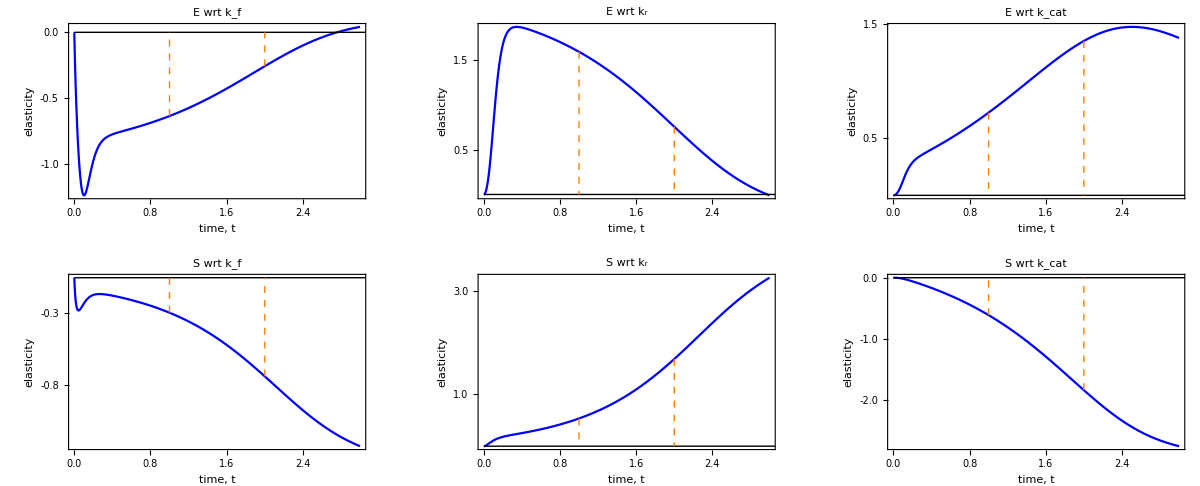

```mathematica
gFinal
```

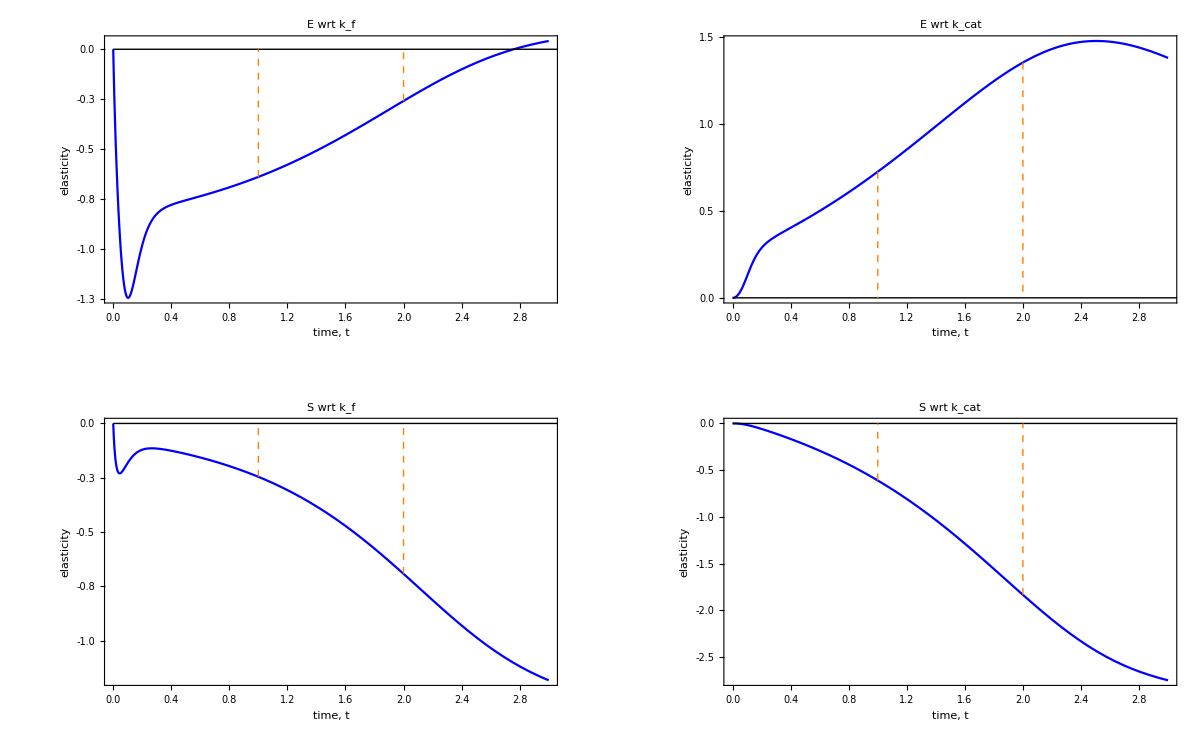

```mathematica
GraphicsGrid[{{gFinal[[1,1]],gFinal[[1,3]]},{gFinal[[2,1]],gFinal[[2,3]]}},ImageSize->1200]
```

```mathematica
Export["../figures/elasticities_MichaelisMenten.pdf",gFinal]
```

elasticities_MichaelisMenten.pdf